```mathematica
delta[values_,begin_,end_]:=(
deltaSum=0;
For[i=begin,i≤end,i++,deltaSum+=(-1)^(end-i - 2)*Binomial[end - 1,i - 1]*values[[i]]];
deltaSum
)
```

```mathematica
newtonForward[n_,x0_,h_,f_]:=(
nNodes=Range[x0,x0+n*h,h];
nValues=f/.x->nNodes;
nT=(x-x0)/h;
nPoly=0;
For[k=1,k≤Length[nValues],k++,nPoly+=delta[nValues,1,k]*Binomial[nT,k -1]];
nPoly//Simplify
)
```

```mathematica
f[x_]=newtonForward[4,1,1,1/(25 +x^2)] //Expand
```

260447/6569225+(483 x)/525538-(321 x^2)/128180+(1113 x^3)/2627690-(613 x^4)/26276900

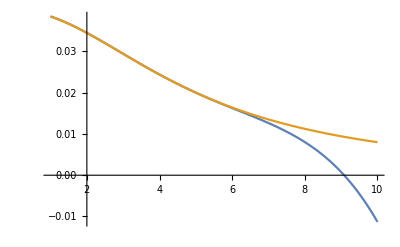

```mathematica
Plot[{f[x],1/(25 +x^2)},{x,1,10}]
```